contact
name : Ahmed Moawad Gharib
email:Dr.gharaib85@gmail.com

## Schrodinger equation

-Graphics-

Schrodinger equation for free particle easily solved symbolically with Mathematica

(∂ ψ[t])/(∂t)= (- i)/ℏ ψ[t]
ψ[t]=c e^(-i h t)

Mathematica return solution with C[1] as initial condition

```mathematica
DSolveValue[ψ'[t]==-ⅈ *h* ψ[t],ψ[t],t]
```

ⅇ^(-ⅈ h t) C[1]

if we specify  initial condition  and Hamiltonian

```mathematica
initialvalue=4;
h=6;
DSolveValue[{ψ'[t]==-ⅈ *h* ψ[t],ψ[0]==initialvalue},ψ[t],t]
```

4 ⅇ^(-6 ⅈ t)

```mathematica
Plot[4Exp[-ⅈ 6 t]//ReIm//Evaluate,{t,0,5},PlotLabels->{"real ","imaginary"}]
```

-Graphics-

#### solve it numerically

NDSolveValue cant accept symbolics every thing is numeric ,initial condition must be known, also time domain must be known

```mathematica
sol=NDSolveValue[{ψ'[t]==-ⅈ *6* ψ[t],ψ[0]==4},ψ,{t,0,5}]
```

InterpolatingFunction[…]

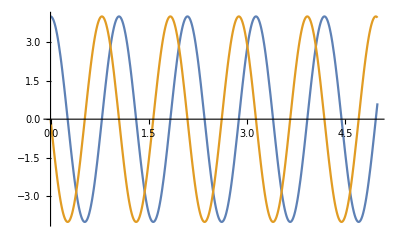

```mathematica
Plot[sol[t]//ReIm//Evaluate,{t,0,5}]
```

### now its time to implement Schrodinger equation solver

```mathematica
ShrodingerSolve[h_,initialvalue_,tf_,t0_:0]:=Block[{ψ},NDSolveValue[{ψ'[t]==-ⅈ *h* ψ[t],ψ[0]==initialvalue},ψ,{t,t0,tf}]]
```

```mathematica
newsol=ShrodingerSolve[6,4,5]
```

InterpolatingFunction[…]

```mathematica
Plot[newsol[t]//ReIm//Evaluate,{t,0,5}]
```

-Graphics-

Mathematica so smart to understand compatibility with Hamiltonian And initial condition
vector space and Bra Ket Dirac notation

```mathematica
ShrodingerSolve[h_?NumberQ,initialvalue_?NumberQ,tf_,t0_:0]:=Block[{ψ},NDSolveValue[{ψ'[t]==-ⅈ *h* ψ[t],ψ[0]==initialvalue},ψ,{t,t0,tf}]];
(*___here h.ψ instead of h*ψ ___*)
ShrodingerSolve[h_?SquareMatrixQ,initialvalue_?ListQ,tf_,t0_:0]:=Block[{ψ},NDSolveValue[{ψ'[t]==-ⅈ *h. ψ[t],ψ[0]==initialvalue},ψ,{t,t0,tf}]];
```

lets solve first example  see qutip-documentation  p52

```mathematica
H=2π*.1*PauliMatrix[1];
ψ0={1,0};
sol=ShrodingerSolve[H,ψ0,10];
```

expectation value
<ψ*|o|ψ>

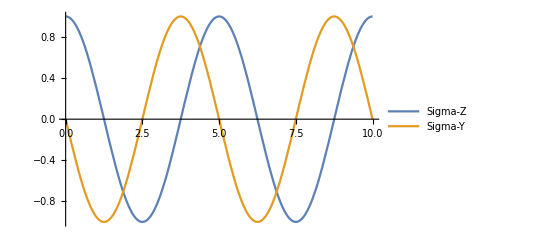

```mathematica
Plot[{sol[t]*.PauliMatrix[3].sol[t],sol[t]*.PauliMatrix[2].sol[t]},{t,0,10},PlotLegends->{"Sigma-Z","Sigma-Y"}]
```

```mathematica
H=2π*.1*PauliMatrix[1];
ψ0={{1},{0}};
sol=ShrodingerSolve[H,ψ0,10];
```

expectation value same as above but insted od conjugate we use conjugate transpost 
but also
we we go beyound and use another forn 
Tr[o.ρ]

```mathematica
rho[t_]:=sol[t].sol[t]†
```

```mathematica
Plot[{Tr[rho[t].PauliMatrix[3]],Tr[rho[t].PauliMatrix[2]]},{t,0,10},PlotLegends->{"Sigma-Z","Sigma-Y"}]
```

-Graphics-

```mathematica
sol[1].sol[1]†
```

{{0.654508+0. ⅈ,0.+0.475528 ⅈ},{0.-0.475528 ⅈ,0.345491+0. ⅈ}}